```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/data_v2/low_mub

```mathematica
dataall=Table[Import["../Shi_low_mu_B/Shi_mu="<>ToString[i]<>"_m0=600.0-flag_4-21x120_VC=true.csv"],{i,0,800,10}];
```

```mathematica
n=Length[Table[i,{i,0,800,10}]]
```

81

```mathematica
dataall[[1]][[1]]
```

{T_mu,sigma,ω₀,n_B,P,e}

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*120+i]][[5]],{i,2,121}],{j,0,20}],{n1,1,81}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[(i-1)*10]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,81}],{j,1,21}];
```

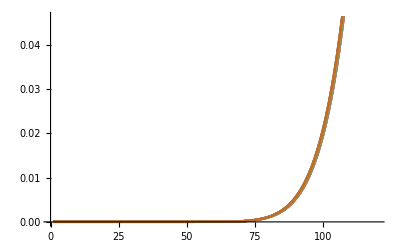

```mathematica
ListLinePlot[pdata[[1]]]
```